Ph. 20 Assignment 5
Grant Messner

1.2)

```mathematica
2+2
```

4

```mathematica
Solve[x^2 -5x+3 == 0,x]
```

{{x→1/2 (5-√13)},{x→1/2 (5+√13)}}

```mathematica
Integrate[Sin[x],{x,0, 1}]
```

1-Cos[1]

```mathematica
f[a_]:=Integrate[Sin[a*x],{x,0, 1}]
```

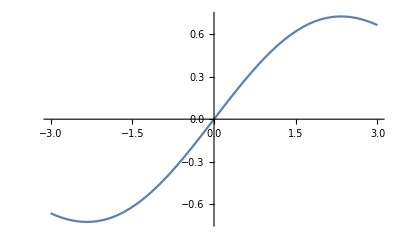

```mathematica
Plot[f[a],{a,-3,3}]
```

```mathematica
Series[Exp[x],{x,0,5}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+O[x]^6

Playing around with some of the tools in Mathematica. Mathematica has the ability to solve equations, integrate and differentiate functions, expand functions into Taylor series, as well as many others.

2.1)

```mathematica
SerCos[x_,n_]:=Normal[Series[Cos[a],{a,0,n}]]/.a->x
```

```mathematica
SerSin[x_,n_]:=Normal[Series[Sin[a],{a,0,n}]]/.a->x
```

```mathematica
SinDiff[x_,n_]:=Sin[x]-SerSin[x,n]
```

```mathematica
CosDiff[x_,n_]:=Cos[x]-SerCos[x,n]
```

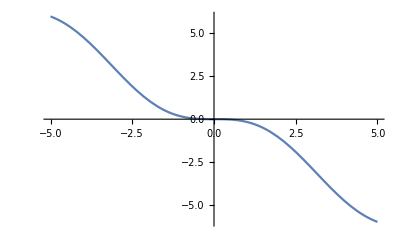

```mathematica
Plot[SinDiff[x,1],{x,-5,5}]
```

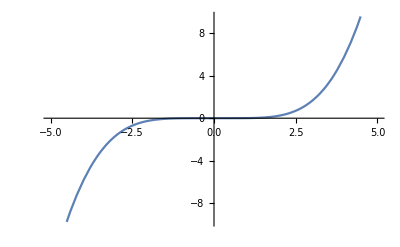

```mathematica
Plot[SinDiff[x,3],{x,-5,5}]
```

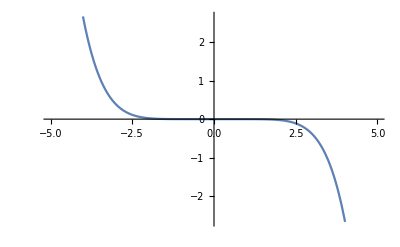

```mathematica
Plot[SinDiff[x,5],{x,-5,5}]
```

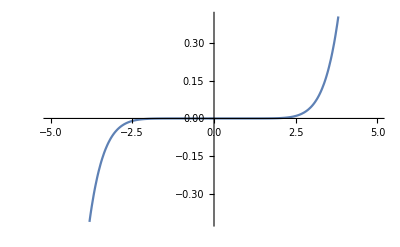

```mathematica
Plot[SinDiff[x,7],{x,-5,5}]
```

Error with respect to the true Sin(x) function for several powers of n (n = 1, 3, 5, 7). As we can see, the error from the true function becomes smaller as the approximation takes on higher powers of n, although the approximation still breaks down for large enough |x| no matter how many powers of n are kept.

2.2)

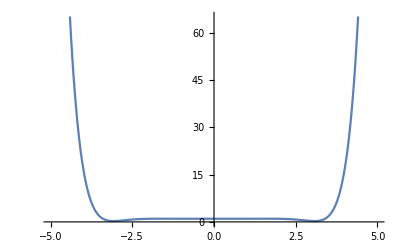

```mathematica
Plot[SerSin[x,5]^2+SerCos[x,5]^2,{x,-5,5}]
```

```mathematica
SerCosSq[x_,n_]:=Normal[Series[Cos[a]^2,{a,0,n}]]/.a->x
```

```mathematica
SerSinSq[x_,n_]:=Normal[Series[Sin[a]^2,{a,0,n}]]/.a->x
```

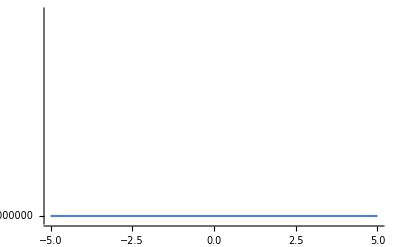

```mathematica
Plot[SerCosSq[x,5]+SerSinSq[x,5],{x,-5,5}]
```

(Top) SerSin[x,5]^2+SerCos[x,5]^2 and (bottom) SerCosSq[x,n] + SerSinSq[x,n] plotted as a function of x. As we can see in the top plot, the series expansions for Cos[x] and Sin[x] blow up for large enough x. This is because the highest order term in each series will be squared (and thus have positive coefficient), and will thus dominate for large enough x and cause the sum to blow up. The SerCosSq[x,n] and SerSinSq[x,n] functions avoid this problem by taking the Taylor expansion of the already squared cosine or sine function.

3.1)

```mathematica
Rx[a_]:={{1,0,0},{0,Cos[a],-Sin[a]},{0,Sin[a],Cos[a]}}
```

```mathematica
Ry[b_]:={{Cos[b],0,Sin[b]},{0,1,0},{-Sin[b],0,Cos[b]}}
```

```mathematica
Rz[c_]:={{Cos[c],-Sin[c],0},{Sin[c],Cos[c],0},{0,0,1}}
```

The rotation matrices defined, using a for theta, b for zeta, and c for phi. The matrices are defined as functions of their respective angles.

3.2)

```mathematica
Rot3[a_,b_,c_]:=Rz[a].Rx[b].Rz[c]
```

```mathematica
FullSimplify[Rz[a].Rx[b].Rz[c]]
```

{{Cos[a] Cos[c]-Cos[b] Sin[a] Sin[c],-Cos[b] Cos[c] Sin[a]-Cos[a] Sin[c],Sin[a] Sin[b]},{Cos[c] Sin[a]+Cos[a] Cos[b] Sin[c],Cos[a] Cos[b] Cos[c]-Sin[a] Sin[c],-Cos[a] Sin[b]},{Sin[b] Sin[c],Cos[c] Sin[b],Cos[b]}}

The Rot3[ψ, θ, φ] matrix defined in terms of a function, with ψ = a, θ = b, φ = c. As we can see, the resulting matrix doesn’t simplify at all!

3.3)

```mathematica
Rot3Inverse[a_,b_,c_]:=Rz[-c].Rx[-b].Rz[-a]
```

```mathematica
FullSimplify[Rot3Inverse[a,b,c].Rot3[a,b,c]]
```

{{1,0,0},{0,1,0},{0,0,1}}

The inverse matrix of Rot3[ψ, θ, φ] defined in terms of a function of ψ = a, θ = b, φ = c. As expected, Rot3Inverse[ψ, θ, φ].Rot3[ψ, θ, φ] simplifies to the identity matrix when we apply FullSimplify to the product.

3.4)

```mathematica
Simplify[Inverse[Rot3[a,b,c]].Rot3[a,b,c]]
```

{{1,0,0},{0,1,0},{0,0,1}}

As expected, inverse matrix of Rot3[ψ, θ, φ] with ψ = a, θ = b, φ = c calculated by Mathematica multiplied by the original Rot3 matrix simplifies to the identity matrix as well.